### Start choosing the example:

```mathematica
t=18;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
```

```mathematica
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{0,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
{B,K,cc,var}=GetKirchhoffMatrix[d2e=Data2Equations[Data/.{I1->10,U1->0,S1->0,S2->0}]];
(crit=CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

It took 0.003138 seconds to preprocess.

System is True

{0.007245,Null}

```mathematica
K//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1)

```mathematica
B//MatrixForm
```

(10
0
0
0
0
0
0)

```mathematica
var
```

{j1,j2,j3,j4,j6,j8,jt1,jt2,jt3,jt4,jt5,jt6}

```mathematica
Length[{j1,j2,j3,j4,j6,j8,jt1,jt2,jt3,jt4,jt5,jt6}]
```

12

```mathematica
Table[1,12]
```

```mathematica
MapThread[Rule,{var,Table[1,12]}]
```

{j1→1,j2→1,j3→1,j4→1,j6→1,j8→1,jt1→1,jt2→1,jt3→1,jt4→1,jt5→1,jt6→1}

```mathematica
AssociationThread[var,cc[var]] /.MapThread[Rule,{var,Table[1,12]}]
```

```mathematica
<|j1->1 1+Abs[(-1+1) IntM[-1+1,1->2]],j2->1 1+Abs[(-1+1) IntM[-1+1,1->2]],j3->1 1+Abs[(-1+1) IntM[-1+1,2->3]],j4->1 1+Abs[(-1+1) IntM[-1+1,2->3]],j6->0,j8->0,jt1->1000000+1 1,jt2->1 1,jt3->1 1,jt4->1 1,jt5->1 1,jt6->1000000+1 1|>
```

<|j1→1,j2→1,j3→1,j4→1,j6→0,j8→0,jt1→1000001,jt2→1,jt3→1,jt4→1,jt5→1,jt6→1000001|>

```mathematica
IntM[-1+1,1->2]
```

0

```mathematica
AssociationThread[var,cc[var]]
```

<|j1→j1 j2+Abs[(-j1+j2) IntM[-j1+j2,1->2]],j2→j1 j2+Abs[(-j1+j2) IntM[-j1+j2,1->2]],j3→j3 j4+Abs[(-j3+j4) IntM[-j3+j4,2->3]],j4→j3 j4+Abs[(-j3+j4) IntM[-j3+j4,2->3]],j6→0,j8→0,jt1→1000000+jt1 jt2,jt2→jt1 jt2,jt3→jt3 jt4,jt4→jt3 jt4,jt5→jt5 jt6,jt6→1000000+jt5 jt6|>

```mathematica
KeySelect[KeyMap[Join[d2e["jvars"],d2e["jtvars"]],d2e["CostArgs"]],MemberQ[var,#]&]
```

<|j1→j1 j2+Abs[(-j1+j2) IntM[-j1+j2,1->2]],j2→j1 j2+Abs[(-j1+j2) IntM[-j1+j2,1->2]],j3→j3 j4+Abs[(-j3+j4) IntM[-j3+j4,2->3]],j4→j3 j4+Abs[(-j3+j4) IntM[-j3+j4,2->3]],j6→0,j8→0,jt1→1000000+jt1 jt2,jt2→jt1 jt2,jt3→jt3 jt4,jt4→jt3 jt4,jt5→jt5 jt6,jt6→1000000+jt5 jt6|>

```mathematica
KeyMap[Join[d2e["jvars"],d2e["jtvars"]],d2e["CostArgs"]]
```

<|j1→j1 j2+Abs[(-j1+j2) IntM[-j1+j2,1->2]],j2→j1 j2+Abs[(-j1+j2) IntM[-j1+j2,1->2]],j3→j3 j4+Abs[(-j3+j4) IntM[-j3+j4,2->3]],j4→j3 j4+Abs[(-j3+j4) IntM[-j3+j4,2->3]],j5→j5 j6+Abs[(-j5+j6) IntM[-j5+j6,3->ex3]],j6→0,j7→j7 j8+Abs[(-j7+j8) IntM[-j7+j8,en1->1]],j8→0,jt1→1000000+jt1 jt2,jt2→jt1 jt2,jt3→jt3 jt4,jt4→jt3 jt4,jt5→jt5 jt6,jt6→1000000+jt5 jt6|>

```mathematica
Join[d2e["jvars"],d2e["jtvars"]]
```

<|{1,1->2}→j1,{2,1->2}→j2,{2,2->3}→j3,{3,2->3}→j4,{3,3->ex3}→j5,{ex3,3->ex3}→j6,{en1,en1->1}→j7,{1,en1->1}→j8,{1,1->2,en1->1}→jt1,{1,en1->1,1->2}→jt2,{2,1->2,2->3}→jt3,{2,2->3,1->2}→jt4,{3,2->3,3->ex3}→jt5,{3,3->ex3,2->3}→jt6|>

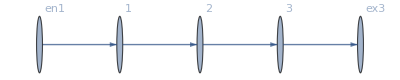

```mathematica
d2e["FG"]
```

#### Non-linear case

```mathematica
alpha = 0.1;
```

```mathematica
alpha = 0.3;
```